```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
κ = 1;
pde = D[u[t,x],{t,2}]-D[u[t,x],{x,2}]+κ^2 u[t,x]==0;
ufun=NDSolveValue[{pde,u[t,0]==0,u[t,1]==0,u[0,x]==1,u[1,x]==0},u,{t,0,1},{x,0,1}];
Plot3D[ufun[t,x],{t,0,1},{x,0,1},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Remove[ufun];
Remove[κ];
pde = D[u[t,x],{t,2}]-D[u[t,x],{x,2}]+κ^2 u[t,x]==0;
ufun=NDSolveValue[{pde,u[t,0]==0,u[t,1]==0,u[0,x]==1,u[1,x]==0},u,{t,0,1},{x,0,1}];
Manipulate[Plot3D[ufun[t,x],{t,0,1},{x,0,1},ColorFunction->"TemperatureMap"],{{κ,1},0,10}]
```

NDSolveValue::femcnsd: The PDE coefficient κ^2 does not evaluate to a numeric scalar at the coordinate {0.5,0.5}; it evaluated to κ^2 instead.

NDSolveValue::dsvar: 0.0000715 cannot be used as a variable.

NDSolveValue::dsvar: 0.0715001 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-(2 (-1+(-1)^k))/(k π)

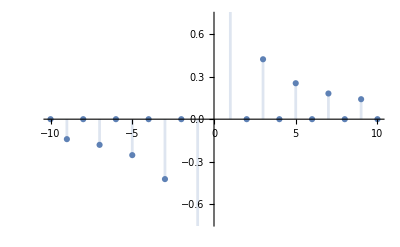

```mathematica
FourierSinCoefficient[1,t,k]
DiscretePlot[%,{k,-10,10}]
```

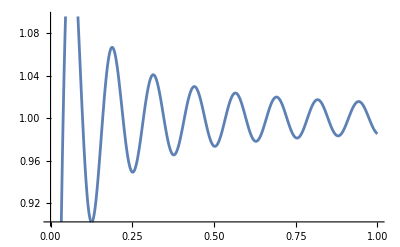

```mathematica
FourierSinSeries[1,x,50];
Plot[%,{x,0,1}]
```

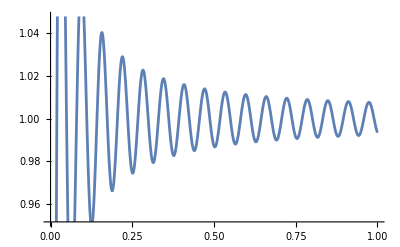

```mathematica
Remove[testfun];
n=100;
testfun[x_] := Sum[-2(-1+((-1)^k))/(k π)*Sin[k x] ,{k,1,n}];
Plot[testfun[x],{x,0,1}]
```

```mathematica
Remove[ufun];
n=100;
kappa = 1.5;
T=2;
ufun[t_,x_]:=Sum[-2(-1+((-1)^k))/(k π Sin[Sqrt[k^2+kappa^2]*T])*Sin[k x] Sin[Sqrt[k^2+kappa^2] (t-T)],{k, 1,n}];
Plot3D[ufun[t,x],{t,0,T},{x,0,2π},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Remove[ufun];
n=100;
kappa = 1.5;
T=2;
ufun[t_,x_]:=Sum[-2(-1+((-1)^k))/(k π Cos[Sqrt[k^2+kappa^2]*T])*Sin[k x] Cos[Sqrt[k^2+kappa^2] (t-T)],{k, 1,n}];
Plot3D[ufun[t,x],{t,0,T},{x,0,2π},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Remove[n,kappa,T];
n=100; (*Define the size of the matrix*)
kappa = 1.5;
T=1;

(*Define matrices and vectors*)
Remove[Ms,Mc,matrixMs,matrixMc,Momega,MomegaSin,MomegaCos,f1,f2];
Ms[i_,j_]:=Sin[i*2π j/n];
matrixMs=Table[Ms[i,j],{i,0,n,1},{j,0,n,1}];
Mc[i_,j_]:=Cos[i*2π j/n];
matrixMc=Table[Mc[i,j],{i,0,n,1},{j,0,n,1}];
Momega[i_,j_]:=Sqrt[i^2+kappa^2]*T*KroneckerDelta[i,j];
MomegaSin=Table[Sin[Momega[i,j]],{i,0,n,1},{j,0,n,1}];
MomegaCos=Table[Cos[Momega[i,j]],{i,0,n,1},{j,0,n,1}];
f1=Table[1,n+1];
f2=Table[0,n+1];

(*Construct augmented matrix and vector*)
augmentedMatrix=ArrayFlatten[{{matrixMc,-matrixMs},{matrixMc.MomegaCos+matrixMs.MomegaSin,matrixMc.MomegaSin-matrixMs.MomegaCos}}];
augmentedVector=Join[f1,f2];

(*Solve the system of linear equations*)
solution=LinearSolve[augmentedMatrix,augmentedVector];

(*Extract x and y from the solution*)
{vc,vs}={solution[[1;;n+1]],solution[[n+2;;2(n+1)]]};

(*Plot the 2D wave solution*)
Remove[ufun];
ufun[t_,x_]:=Re[Sum[(vc[[k+1]]+I*vs[[k+1]])*Exp[I(k x-Sqrt[k^2+kappa^2] t) ],{k, 0,n}]];
Plot3D[ufun[t,x],{t,0,T},{x,0,2π},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Remove[n,kappa,T];
n=3; (*Define the size of the matrix*)
kappa = 1;
T=1;
(*Define the inner product*)
innerProduct[f_,g_,{t_,a_,b_}]:=Integrate[Conjugate[f] g,{t,a,b}]

(*Define the set of functions*)
functions = Table[Exp[I Sqrt[k^2+kappa^2]t],{k,0,n,1}];

(*Compute the inner products to make the basis orthogonal*)
orthogonalBasis=Orthogonalize[functions,innerProduct[#1,#2,{t,0,T}]&];
orthogonalBasis//MatrixForm;

(*Normalize the orthogonal basis*)
orthonormalBasis=Normalize[orthogonalBasis,innerProduct[#,{t,0,T}]&];
```

(1
(-ⅈ+ⅇ^(ⅈ t)+ⅈ Cos[1]-Sin[1])/(√(-1+2 Cos[1]))
√((-1+2 Cos[1])/((1-Sin[1]) (-3+4 Cos[1]+Sin[1]))) (ⅇ^(2 ⅈ t)+(2 ⅇ^(ⅈ/2) Sin[1/2] (-ⅈ+ⅇ^(ⅈ t)+ⅈ Cos[1]-Sin[1]) (-1+Sin[1]))/(-1+2 Cos[1])-ⅇ^ⅈ Sin[1])
6 (1/3 ⅈ (-1+ⅇ^(3 ⅈ))+ⅇ^(3 ⅈ t)-(ⅇ^ⅈ (-ⅈ+ⅇ^(ⅈ t)+ⅈ Cos[1]-Sin[1]) (-2 Cos[1]+2 Cos[2]+3 Sin[1]))/(3 (-1+2 Cos[1]))+(ⅇ^(ⅈ/2) Sin[1/2] (ⅇ^(2 ⅈ t)+(2 ⅇ^(ⅈ/2) Sin[1/2] (-ⅈ+ⅇ^(ⅈ t)+ⅈ Cos[1]-Sin[1]) (-1+Sin[1]))/(-1+2 Cos[1])-ⅇ^ⅈ Sin[1]) (3-16 Cos[1]+7 Cos[2]+8 Sin[1]+2 Sin[2]))/(3 (1-Sin[1]) (-3+4 Cos[1]+Sin[1]))) √((2 (-1+Sin[1]) (-3+4 Cos[1]+Sin[1]))/(29+416 Cos[1]-676 Cos[2]+160 Cos[3]-Cos[4]-672 Sin[1]+192 Sin[2]+96 Sin[3])))

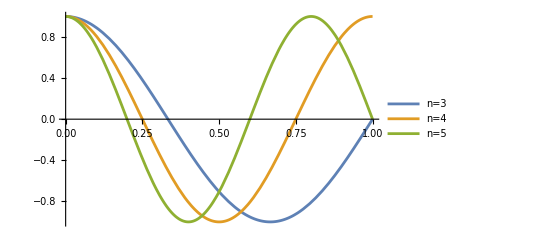

```mathematica
T=1;
Plot[{Cos[ 3π t/2/T],Cos[4 π t/2/T],Cos[5 π t/2/T]},{t,0,T}, PlotLegends->{"n=3","n=4","n=5"}]
```